Benzene for molecular electronics
Hernández-Montes Omar
e-mail: omar.hdz.mon@gmail.com

```mathematica
Clear[G,T,Gn,Tbond]
thopCC=1.0;
thopCN = -2.79;
eonsiteC=0;
eonsiteN=-1.89;
eonsiteCl=-4.92;
thopClC=-2.25;
η=0.01;
Hbenzene=SparseArray[{{i_,i_}->eonsiteC,{i_,j_}/;Abs[i-j]==1->thopCC,{i_,j_}/;Abs[i-j]==5->thopCC},{6,6}];
Σs[nat_,conectionL_]:=-I*SparseArray[{i_,i_}/;Abs[i-conectionL]==0->η,{nat,nat}];
Σd[nat_,conectionR_]:=-I*SparseArray[{i_,i_}/;Abs[i-conectionR]==0->η,{nat,nat}];
Vgate[nat_,vg_]:=SparseArray[{{i_,i_}->vg},{nat,nat}];
G[ϵ_,nat_,conectionL_,conectionR_,vg_,Hc_]:=Chop[Inverse[ϵ*IdentityMatrix[nat]-Hc-Σs[nat,conectionL]-Σd[nat,conectionR]-Vgate[nat,vg]]];
Γs[nat_,conectionL_]:=I*(Σs[nat,conectionL]-Transpose[Conjugate[Σs[nat,conectionL]]]);
Γd[nat_,conectionR_]:=I*(Σd[nat,conectionR]-Transpose[Conjugate[Σd[nat,conectionR]]]);
Tmatrix[ϵ_,nat_,conectionL_,conectionR_,vg_,Hc_]:=Chop[Γs[nat,conectionL].#.Γd[nat,conectionR].Transpose[Conjugate[#]]]&@G[ϵ,nat,conectionL,conectionR,vg,Hc];
T[ϵ_,nat_,conectionL_,conectionR_,vg_,Hc_]:=Tr[Tmatrix[ϵ,nat,conectionL,conectionR,vg,Hc]];
(*For bond transmission*)
Gn[ϵ_,nat_,conectionL_,conectionR_,vg_,Hc_]:=2Chop[#.Im[Σs[nat,conectionR]].Transpose[Conjugate[#]]]&@G[ϵ,nat,conectionL,conectionR,vg,Hc];
Tbond[ϵ_,nat_,conectionL_,conectionR_,vg_,Hc_,j_,k_]:=Im[Conjugate[Hc[[j,k]]]*Gn[ϵ,nat,conectionL,conectionR,vg,Hc][[j,k]]];
```

```mathematica
Tbondpara= N[Table[Tbond[0,6,1,4,0,Hbenzene,i,j],{i,1,6},{j,1,6}]];
Tbondmeta= N[Table[Tbond[0,6,1,3,0,Hbenzene,i,j],{i,1,6},{j,1,6}]];
MatrixForm[Diagonal[Tbondpara,1]]
MatrixForm[Diagonal[Tbondmeta,1]]
```

(0.0000249988
0.0000249988
0.0000249988
-0.0000249988
-0.0000249988)

(0.
0.
0.
0.
0.)

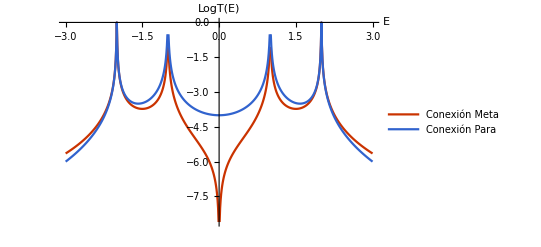

```mathematica
mbenzene1=ParallelTable[{ϵ,Log10[T[ϵ,6,1,3,0,Hbenzene]]},{ϵ,-3,3,0.01}];
pbenzene1=ParallelTable[{ϵ,Log10[T[ϵ,6,1,4,0,Hbenzene]]},{ϵ,-3,3,0.01}];
ListLinePlot[{mbenzene1,pbenzene1},PlotLegends->{"Conexión Meta","Conexión Para"},AxesLabel->{"E","LogT(E)"},PlotStyle->112]
```

```mathematica
mbenzene2=ParallelTable[{ϵ,Log10[T[ϵ,6,1,3,-0.5,Hbenzene]]},{ϵ,-3,3,0.01}];
mbenzene3=ParallelTable[{ϵ,Log10[T[ϵ,6,1,3,0.5,Hbenzene]]},{ϵ,-3,3,0.01}];
ListLinePlot[{mbenzene1,mbenzene2,mbenzene3},PlotLegends->{"Vg = 0V","Vg = -0.5V","Vg = 0.5V"},AxesLabel->{"E","LogT(E)"},PlotStyle->112]
```

```mathematica
currentm[vsd_,vg_]:=NIntegrate[Hold[T[ϵ,6,1,3,vg,Hbenzene]],{ϵ,-vsd/2,vsd/2}];
currentm1=ParallelTable[{vsd,currentm[vsd,0]},{vsd,0.0,2.5,0.02}];
currentm2=ParallelTable[{vsd,currentm[vsd,0.5]},{vsd,0.0,2.5,0.02}];
currentm3=ParallelTable[{vsd,currentm[vsd,1.0]},{vsd,0.0,2.5,0.02}];
currentm4=ParallelTable[{vsd,currentm[vsd,2.0]},{vsd,0.0,2.5,0.02}];
```

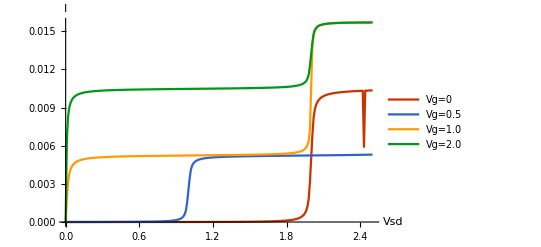

```mathematica
ListLinePlot[{currentm1,currentm2,currentm3,currentm4},PlotLegends->{"Vg=0","Vg=0.5","Vg=1.0","Vg=2.0"},AxesLabel->{"Vsd","I"},PlotStyle->112]
```

```mathematica
currentp[vsd_,vg_]:=NIntegrate[Hold[T[ϵ,6,1,4,vg,Hbenzene]],{ϵ,-vsd/2,vsd/2}];
currentp1=ParallelTable[{vsd,currentp[vsd,0]},{vsd,0.0,2.5,0.02}];
currentp2=ParallelTable[{vsd,currentp[vsd,0.5]},{vsd,0.0,2.5,0.02}];
currentp3=ParallelTable[{vsd,currentp[vsd,1.0]},{vsd,0.0,2.5,0.02}];
currentp4=ParallelTable[{vsd,currentp[vsd,2.0]},{vsd,0.0,2.5,0.02}];
```

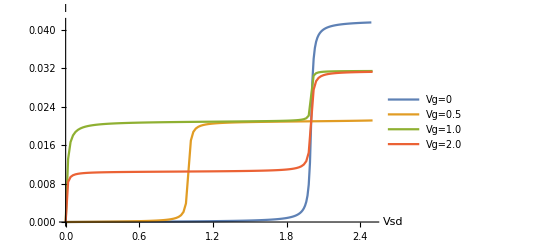

```mathematica
ListLinePlot[{currentp1,currentp2,currentp3,currentp4},PlotLegends->{"Vg=0","Vg=0.5","Vg=1.0","Vg=2.0"},AxesLabel->{"Vsd","I"}]
```